```mathematica
ClearAll["Global`*"]
```

```mathematica
IP[λ_,σ_,ρ_,μ_,α_,β_,ϵ_] :=ItoProcess[{
ⅆF[t]== (λ*F[t]-σ*(1-R[t])*F[t] + ρ*R[t]*H[t])ⅆt ,
ⅆH[t]== (σ*(1-R[t])*F[t] - ρ*R[t]*H[t] - μ*H[t])ⅆt ,
ⅆR[t]==(α*ⅆt+ϵ*ⅆW[t])*R[t]*(1-R[t]) - R[t]*(ρ*H[t] + β*F[t])ⅆt},
{F[t],H[t],R[t]},
{{F,H,R},{0.15,0.15,0.15}},
t,
W\[Distributed]WienerProcess[]
]
```

```mathematica
IP[ λ,σ,ρ,μ,α,β,ϵ]
```

ItoProcess[{{λ F[t]-σ F[t]+σ F[t] R[t]+ρ H[t] R[t],σ F[t]-μ H[t]-σ F[t] R[t]-ρ H[t] R[t],α R[t]-β F[t] R[t]-ρ H[t] R[t]-α R[t]^2},{{0},{0},{ϵ R[t]-ϵ R[t]^2}},{F[t],H[t],R[t]}},{{F,H,R},{0.15,0.15,0.15}},{t,0}]

```mathematica
stochsol[T_,TSlice_,Iterations_, λ_,σ_,ρ_,μ_,α_,β_,ϵ_]:=RandomFunction[IP[ λ,σ,ρ,μ,α,β,ϵ],{0,T,TSlice},Iterations,Method->"KloedenPlatenSchurz"];
TD = With[{T=200,TSlice=0.05,Iterations=5,λ=0.2,σ=0.8,ρ=0.2,μ=0.3,α=0.5,β=0.2,ϵ=0.1},
stochsol[T,TSlice,Iterations,λ,σ,ρ,μ,α,β,ϵ]
]["PathComponents"];
```

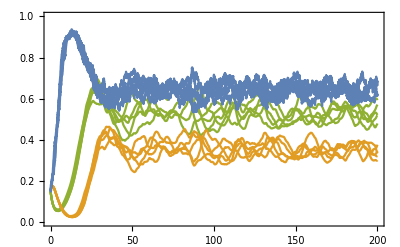

```mathematica
Show[{Table[ListLinePlot[TD[[i]],PlotStyle->ColorData[97,4-i],PlotRange->{0,1},Frame->True],{i,1,3}]}]
```

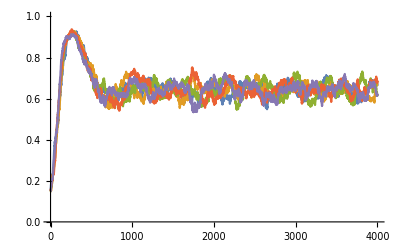

```mathematica
ListLinePlot[TD[[3]][[2]][[1]][[1;;5]],PlotRange->{0,1}]
```